```mathematica
Ereal[t_]:=a Cos[ω1 t]+b Cos[ω2 t]
```

```mathematica
(Ereal[t]+Ereal[t+τ])^2//Expand
```

a^2 Cos[t ω1]^2+2 a^2 Cos[t ω1] Cos[(t+τ) ω1]+a^2 Cos[(t+τ) ω1]^2+2 a b Cos[t ω1] Cos[t ω2]+2 a b Cos[(t+τ) ω1] Cos[t ω2]+b^2 Cos[t ω2]^2+2 a b Cos[t ω1] Cos[(t+τ) ω2]+2 a b Cos[(t+τ) ω1] Cos[(t+τ) ω2]+2 b^2 Cos[t ω2] Cos[(t+τ) ω2]+b^2 Cos[(t+τ) ω2]^2

```mathematica
Ecompl[t_]:=a Exp[I ω1 t]+b Exp[I ω2 t]
```

```mathematica
Esum=Ecompl[t]+Ecompl[t+τ]
```

a ⅇ^(ⅈ t ω1)+a ⅇ^(ⅈ (t+τ) ω1)+b ⅇ^(ⅈ t ω2)+b ⅇ^(ⅈ (t+τ) ω2)

```mathematica
EsumCC=Esum/.{ω1->-ω1,ω2->-ω2}
```

a ⅇ^(-ⅈ t ω1)+a ⅇ^(-ⅈ (t+τ) ω1)+b ⅇ^(-ⅈ t ω2)+b ⅇ^(-ⅈ (t+τ) ω2)

```mathematica
Esum EsumCC//Expand//FullSimplify
```

2 (a^2+b^2+a^2 Cos[τ ω1]+b (b Cos[τ ω2]+a (Cos[t (ω1-ω2)]+Cos[(t+τ) (ω1-ω2)]+Cos[(t+τ) ω1-t ω2]+Cos[t ω1-(t+τ) ω2])))

Too triggy too quickly

```mathematica
Esum EsumCC//Expand//FullSimplify
```

2 (a^2+b^2+a^2 Cos[τ ω1]+b (b Cos[τ ω2]+a (Cos[t (ω1-ω2)]+Cos[(t+τ) (ω1-ω2)]+Cos[(t+τ) ω1-t ω2]+Cos[t ω1-(t+τ) ω2])))

Throw out any term with a t in it, because that oscillates too fast. Keep terms with only a τ

```mathematica
Iavg=4+ⅇ^(-ⅈ τ ω1)+ⅇ^(ⅈ τ ω1)+ⅇ^(-ⅈ τ ω2)+ⅇ^(ⅈ τ ω2)
```

4+ⅇ^(-ⅈ τ ω1)+ⅇ^(ⅈ τ ω1)+ⅇ^(-ⅈ τ ω2)+ⅇ^(ⅈ τ ω2)

```mathematica
Iavg=2 (a^2+b^2+a^2 Cos[τ ω1]+b^2 Cos[τ ω2])
```

2 (a^2+b^2+a^2 Cos[τ ω1]+b^2 Cos[τ ω2])

```mathematica
Iavg=Iavg//FullSimplify
```

2 (a^2+b^2+a^2 Cos[τ ω1]+b^2 Cos[τ ω2])

```mathematica
Iavg/.{ω1->ω-Δω/2,ω2->ω+Δω/2}//TrigExpand
```

4+2 Cos[τ (-Δω/2+ω)]+2 Cos[τ (Δω/2+ω)]

Use Cos[a+b]=Cos[a]Cos[b]-Sin[a]Sin[b]

```mathematica
4+2( Cos[ω τ]Cos[Δω/2 τ]-Sin[ω τ]Sin[Δω/2 τ]+Cos[ω τ]Cos[Δω/2 τ]+Sin[ω τ]Sin[Δω/2 τ])
```

4+4 Cos[(Δω τ)/2] Cos[τ ω]

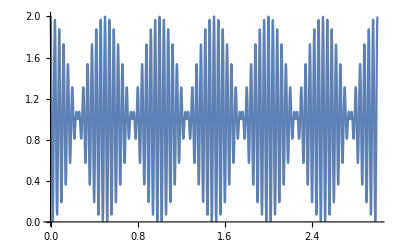

```mathematica
Plot[1+ Cos[Δω τ] Cos[τ ω]/.{ω->2π 25,Δω->2π},{τ,0,3}]
```

```mathematica
Solve[(Δω τ)/2==π/.{τ->(2d)/c,Δω->(2π c)/λ1-(2π c)/λ2},d]//Simplify
```

{{d→-(λ1 λ2)/(2 (λ1-λ2))}}

```mathematica
-(λ1 λ2)/(2 (λ1-λ2))==1/(2/λ1-2/λ2)//Simplify
```

True

```mathematica
1/(2/λ1-2/λ2)/.{λ1-> 589.0*^-9,λ2-> 589.6*^-9}
```

0.000289395